```mathematica
Clear["Global`*"]
```

Distribution of hedge (Proposition 1 in Notes)

Copula function 
The Binormal copula distribution implementation in Mathematica does not work very well, so best to implement directly.

```mathematica
Ncdf[x_]:=CDF[NormalDistribution[],x]
Ninv[p_]:=InverseCDF[NormalDistribution[],p]
```

```mathematica
CSF[u_,v_]:=CDF[CopulaDistribution[{"Binormal", 0.9}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}],{u,v}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
```

```mathematica
CSF[u_,v_]:=CDF[CopulaDistribution[{"GumbelHougaard", 2}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}],{u,v}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
```

### Gaussian copula - Normal margins

```mathematica
ρ=0.9;
CSF[u_,v_]:=CDF[BinormalDistribution[{0,0}, {1,1},ρ],{InverseCDF[NormalDistribution[],u],InverseCDF[NormalDistribution[],v]}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
h=1;
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
Fh[0.5]
```

0.868224

```mathematica
CDF[NormalDistribution[0,Sqrt[1+h-2 ρ h]],0.5]
```

0.868224

```mathematica
t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];
```

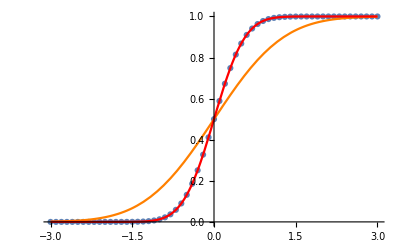

```mathematica
Show[
ListPlot[t, PlotStyle->Large],
Plot[Ncdf[x], {x,-3,3},PlotStyle->Orange],
Plot[CDF[NormalDistribution[0,Sqrt[1+h - 2 ρ h]],x], {x,-3,3}, PlotStyle->Red] 
]
```

### Gaussian copula - non-Normal margins

```mathematica
ρ=0.9;
CSF[u_,v_]:=CDF[BinormalDistribution[{0,0}, {1,1},ρ],{InverseCDF[NormalDistribution[],u],InverseCDF[NormalDistribution[],v]}]
FS[x_]:=CDF[ExponentialDistribution[1],x]
FF[x_]:=CDF[StudentTDistribution[10],x]
FSInv[p_]:=InverseCDF[ExponentialDistribution[1],p]
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
Fh2[x_]:=1-NIntegrate[Ncdf[(Ninv[FF[(FSInv[w]-x)/h]]-ρ Ninv[w])/(√(1-ρ^2))], {w,0,1}]
```

```mathematica
Timing[Fh[0.5]]
```

{0.758957,0.207144}

```mathematica
Timing[Fh2[0.5]]
```

{0.028624,0.207144}

```mathematica
X1=RandomVariate[ExponentialDistribution[1],10000];
X2=RandomVariate[StudentTDistribution[10],10000];
Y1=Ninv[CDF[ExponentialDistribution[1],X1]];
Y2=Ninv[CDF[StudentTDistribution[10],X2]];
RS=X1;
RF = ρ Y1 + Sqrt[1-ρ^2] Y2;
Z=RS-h RF;
```

```mathematica
Timing[t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{29.3806,Null}

```mathematica
Timing[t2=Table[{x,Fh2[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.93996,Null}

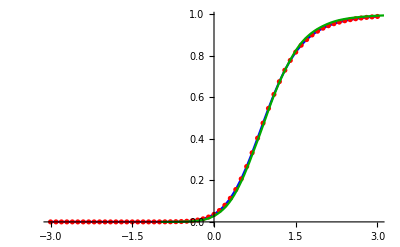

```mathematica
Show[
ListPlot[{t,t2},PlotStyle->{Blue,Red}, Joined->{True,False}],
SmoothHistogram[Z,Automatic,"CDF", PlotStyle->Darker[Green]]
]
```

### Student t copula - Student t margins

The Student t distribution arises as a normal variance mixture where the mixing variable is inverse gamma with parameter 1/2 ν, 1/2 ν.

```mathematica
ρ=0.9;
ν=10;
h=1;
CSF[u_,v_]:=CDF[MultivariateTDistribution[{0,0}, {{1,ρ},{ρ,1}},ν],{InverseCDF[StudentTDistribution[ν],u],InverseCDF[StudentTDistribution[ν],v]}]
FS[x_]:=N[CDF[StudentTDistribution[ν],x]]
FF[x_]:=N[CDF[StudentTDistribution[ν],x]]
FSInv[p_]:=N[InverseCDF[StudentTDistribution[ν],p]]
```

```mathematica
detsq:=Det[{{1,ρ}, {ρ,1}}]^(1/2)
matp:=MatrixPower[{{1,ρ}, {ρ,1}},-1]
PDFBivariateT[x_,y_]:=NIntegrate[w^(-1)/((2 Pi)detsq) Exp[-({x,y}.matp.{x,y})/(2 w)] PDF[InverseGammaDistribution[1/2 ν, 1/2 ν],w], {w,0,∞}]
```

```mathematica
detsq:=Det[{{1,ρ}, {ρ,1}}]^(1/2)
matp:=MatrixPower[{{1,ρ}, {ρ,1}},-1]
α=1/2 ν;
β = 1/2 ν;
pdfig[x_]:=β^α / Gamma[α] x^(-α-1) Exp[-β/x];
PDFBivariateT[x1_,y1_]:=NIntegrate[w^(-1)/((2 Pi)detsq) Exp[-({x1,y1}.matp.{x1,y1})/(2 w)] pdfig[w], {w,0,∞}]
```

```mathematica
CDFBivariateT[x_,y_]:=NIntegrate[PDFBivariateT[z1,z2],{z2,-∞,y}, {z1,-∞,x}]
CDFBivariateT[x_,y_]:=NIntegrate[w^(-1)/((2 Pi)detsq) Exp[-({z1,z2}.matp.{z1,z2})/(2 w)] pdfig[w], {w,0,∞},{z2,-∞,y}, {z1,-∞,x}]
```

```mathematica
{Timing[PDFBivariateT[.5,.5]], Timing[PDF[MultivariateTDistribution[{{1,ρ}, {ρ,1}}, ν],{.5,.5}]]}
```

(0.019733 | 0.312433
0.001288 | 0.312433)

```mathematica
{Timing[PDFBivariateT[0,0]], Timing[PDF[MultivariateTDistribution[{{1,ρ}, {ρ,1}}, ν],{0,0}]]}
```

(0.006905 | 0.365126
0.000414 | 0.365126)

```mathematica
TimeConstrained[{Timing[CDFBivariateT[0,0]], Timing[CDF[MultivariateTDistribution[{{1,ρ}, {ρ,1}}, ν],{0,0}]]},30]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(1.77782 | 0.428216
0.000585 | 0.428217)

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
TimeConstrained[Fh[0.5],30]
```

$Aborted

```mathematica
TimeConstrained[Simplify[CSF[0.5, FF[(FSInv[w2]-1)/h]]/.Sign->RealSign]/.w2->w,30]
```

$Aborted

```mathematica
TimeConstrained[tmp[w1_,w2_]=Simplify[D[CSF[w,w2],w]/.Sign->RealSign]/.w->w1,30]
```

$Aborted

```mathematica
TimeConstrained[D[Simplify[CSF[w,FF[(FSInv[w2]-1)/h]]/.Sign->RealSign],w]/.{w2->w, w->.5},30]
```

$Aborted

```mathematica
TimeConstrained[CSF[w,FF[(FSInv[w2]-1)/h]]/.{w2->0.5,w->0.5},30]
```

0.168725

```mathematica
DCSF[x_,w_,w2_]:=Simplify[D[CSF[w1,FF[(FSInv[w2]-x)/h]]/.Sign->RealSign,w1]/.w1->w]
```

```mathematica
TimeConstrained[Timing[DCSF[0.5, 0.5, 0.2]], 30]
```

{0.016161,0.00342659}

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]]/.Sign->RealSign,w]/.w2->w], {w,0,1}]
```

```mathematica
Fh[x_]:=1-NIntegrate[DCSF[x,w,w], {w,0,1.}]
```

```mathematica
TimeConstrained[Timing[Fh[0.5]],30]
```

$Aborted

```mathematica
Fh2[x_]:=CDF[StudentTDistribution[0,Sqrt[1+h^2-2 ρ h],ν], x]
```

```mathematica
Fh2[0.5]
```

0.855154

```mathematica
z=RandomVariate[MultivariateTDistribution[{0,0}, {{1,ρ},{ρ,1}},ν], 2000];
rh = z[[;;,1]] - h z[[;;,2]];
```

```mathematica
CDF[SmoothKernelDistribution[rh],0.5]
```

0.85787

```mathematica
t=Table[DCSF[x, w,w],{x,-2,2,0.25}, {w,0,1,0.01}];
t2=1-Total[t[[;;,;;-2]]ᵀ]0.01;
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

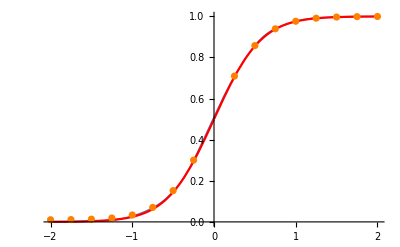

```mathematica
Show[
Plot[CDF[SmoothKernelDistribution[rh], x], {x,-2,2},PlotStyle->Thick],
Plot[Fh2[x], {x,-2,2},PlotStyle->Red],
ListPlot[t2, DataRange->{-2,2},PlotStyle->Orange]
]
```

### Student t copula - non-Student t margins

```mathematica
ρ=0.9;
ν=10;
h=1;
CSF[u_,v_]:=CDF[MultivariateTDistribution[{0,0}, {{1,ρ},{ρ,1}},ν],{InverseCDF[StudentTDistribution[ν],u],InverseCDF[StudentTDistribution[ν],v]}]
FS[x_]:=CDF[ExponentialDistribution[1],x]
FF[x_]:=CDF[StudentTDistribution[10],x]
FSInv[p_]:=InverseCDF[ExponentialDistribution[1],p]
FFInv[p_]:=InverseCDF[StudentTDistribution[10],p]
V[x_]:=CDF[StudentTDistribution[ν],x]
VInv[p_]:=InverseCDF[StudentTDistribution[ν],p]
Ncdf[x_]:=CDF[NormalDistribution[],x]
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

-Graphics-

```mathematica
TimeConstrained[Timing[Fh[0.5]],30]
```

$Aborted

The interpolation functions do now work well in numerical integration because of the oscillations.

```mathematica
iV=Interpolation[Table[{x,V[x]}, {x,VInv[0.001],VInv[0.999],0.25}],InterpolationOrder->5];
```

```mathematica
{FFInv[0.001], FFInv[0.999]}
```

{-4.1437,4.1437}

```mathematica
iFF=Interpolation[Table[{x,FF[x]}, {x, FFInv[0.001], FFInv[0.999], 0.25}],InterpolationOrder->5];
```

InterpolatingFunction::dmval: Input value {-5.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

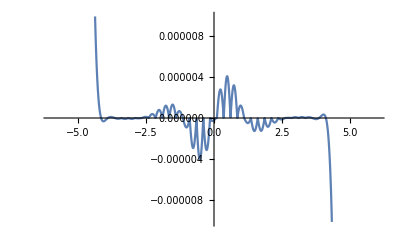

```mathematica
Plot[{V[x]-iV[x]}, {x,-6,6}]
```

```mathematica
Plot[{FF[x]-iFF[x]}, {x,-6,6}]
```

InterpolatingFunction::dmval: Input value {-5.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

AccuracyGoal can be used to speed up computations for optimisation

```mathematica
Fh2[x_]:=1-NIntegrate[Ncdf[(VInv[FF[(FSInv[V[Sqrt[w] z]]-x)/h]]-ρ Sqrt[w] z)/(Sqrt[w] √(1-ρ^2))]PDF[NormalDistribution[],z] PDF[InverseGammaDistribution[ν/2,ν/2],w],{z,-4,4},{w,0,∞},AccuracyGoal->2]
```

```mathematica
TimeConstrained[Timing[Fh2[0.5]],30]
```

{5.26207,0.200346}

Without AccuracyGoal

```mathematica
(*TimeConstrained[Timing[Fh2[0.5]],30]*)
```

{12.5572,0.200772}

```mathematica
n=100;
Timing[Table[VInv[x], {x,0,1,1/n}];]
```

{0.105248,Null}

```mathematica
Timing[Table[FSInv[x], {x,0,1,1/n}];]
```

{0.003034,Null}

```mathematica
Timing[Table[FF[x], {x,-4,4,(4-(-4))/n}];]
```

{0.973381,Null}

```mathematica
Timing[Table[V[x], {x,-4,4,(4-(-4))/n}];]
```

{1.00704,Null}

```mathematica
Timing[Table[iV[x], {x,-4,4,(4-(-4))/n}];]
```

InterpolatingFunction::dmval: Input value {-4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-98/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-96/25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.005768,Null}

```mathematica
W=RandomVariate[InverseGammaDistribution[1/2ν, 1/2ν], 10000];
Z=RandomVariate[NormalDistribution[],{10000,2}];
T= √W Transpose[{Z⟦1;;All,1⟧,ρ Z⟦1;;All,1⟧+√(1-ρ^2) Z⟦1;;All,2⟧}];
```

```mathematica
RS=FSInv[V[T⟦1;;All,1⟧]];
RF=FFInv[V[T⟦1;;All,2⟧]];
Rh = RS - h RF;
```

```mathematica
TimeConstrained[Timing[Fh2[-3]],30]
```

{5.47533,-0.00106498}

```mathematica
Timing[t=Table[{x,Fh2[x]}, {x,-3,3, 0.2}];]
```

{164.274,Null}

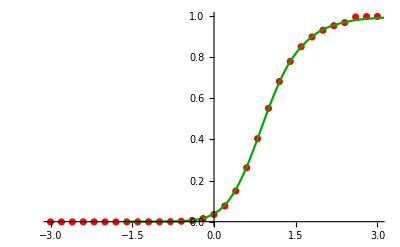

```mathematica
Show[
ListPlot[t, PlotStyle->Red],
SmoothHistogram[Rh,Automatic,"CDF", PlotStyle->Darker[Green]]
]
```